```mathematica
loadtimeseriesResampled=Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\LoadtimeseriesResampled.wxf"]
```

TimeSeries[…]

```mathematica
Min[loadtimeseriesResampled]
```

8664.59

```mathematica
Max[loadtimeseriesResampled]
```

27376.7

### Forecasting with Fully Scaled Data

```mathematica
loadmodelfit=TimeSeriesModelFit[loadtimeseriesResampled]
```

TimeSeriesModel[…]

```mathematica
loadmodelfit["ParameterTable"]
```

General::munfl: 6.628959565280767552514×10^-12373 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.269616311694080793446×10^-3517 is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
𝒶_1 | 1.64257 | 0.00529501 | 310.211 | 0.
𝒶_2 | -0.697632 | 0.00511084 | -136.501 | 0.
𝒷_1 | -0.131058 | 0.00634279 | -20.6625 | 8.18371×10^-95
𝒷_2 | 0.159042 | 0.00513928 | 30.9464 | 6.83169×10^-209

```mathematica
forecast=TimeSeriesForecast[loadmodelfit,{72}]
```

TemporalData[…]

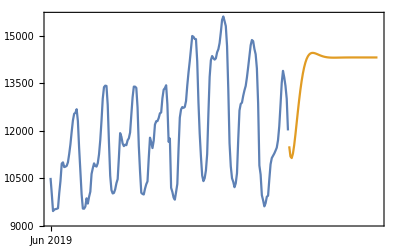

```mathematica
tsmodelDLP=DateListPlot[{TimeSeriesWindow[loadtimeseriesResampled,{DateObject[{2019,6,1}],DateObject[{2019,8,24}]}],forecast}]
```

### Forecasting with Min Subtracted Data

```mathematica
subtractedTS=Subtract[loadtimeseriesResampled,Min[loadtimeseriesResampled]]
```

TimeSeries[…]

```mathematica
subtractedloadmodelfit=TimeSeriesModelFit[subtractedTS]
```

TimeSeriesModel[…]

```mathematica
subtractedloadmodelfit["ParameterTable"]
```

General::munfl: 6.628959531097559317146×10^-12373 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.269616297108731797089×10^-3517 is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
𝒶_1 | 1.64257 | 0.00529501 | 310.211 | 0.
𝒶_2 | -0.697632 | 0.00511084 | -136.501 | 0.
𝒷_1 | -0.131058 | 0.00634279 | -20.6625 | 8.18371×10^-95
𝒷_2 | 0.159042 | 0.00513928 | 30.9464 | 6.83169×10^-209

```mathematica
subtractedforecast=TimeSeriesForecast[subtractedloadmodelfit,{72}]
```

TemporalData[…]

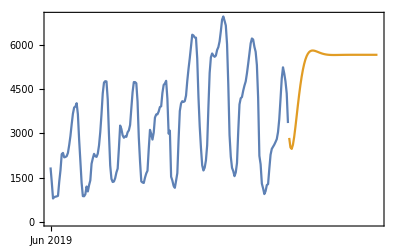

```mathematica
subtractedtsmodelDLP=DateListPlot[{TimeSeriesWindow[subtractedTS,{DateObject[{2019,6,1}],DateObject[{2019,8,24}]}],subtractedforecast}]
```

```mathematica
loadTSModelSARIMA=TimeSeriesModelFit[loadtimeseriesResampled,{"SARIMA",{Automatic,Automatic,Automatic}}]
```

TimeSeriesModel[…]

```mathematica
loadTSModelSARIMA["ParameterTable"]
```

General::munfl: 6.628959543894123001194×10^-12373 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.269616302278222576726×10^-3517 is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
𝒶_1 | 1.64257 | 0.00529501 | 310.211 | 0.
𝒶_2 | -0.697632 | 0.00511084 | -136.501 | 0.
𝒷_1 | -0.131058 | 0.00634279 | -20.6625 | 8.18371×10^-95
𝒷_2 | 0.159042 | 0.00513928 | 30.9464 | 6.83169×10^-209

```mathematica
loadSubtractedTSModelSARIMA=TimeSeriesModelFit[subtractedTS,{"SARIMA",{Automatic,Automatic,Automatic}}]
```

TimeSeriesModel[…]

```mathematica
rescaledSubtractedTS=Rescale[subtractedTS]
```

TimeSeries[…]

```mathematica
Export["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\rescaledsubtractedTS.wxf", rescaledSubtractedTS]
```

C:\Users\kylem\Documents\GitHub\2019-WSS\Final Project\Drafts\kyle\rescaledsubtractedTS.wxf

```mathematica
Min[rescaledSubtractedTS]
```

0.

```mathematica
Max[rescaledSubtractedTS]
```

1.

```mathematica
rescaledSubtractedloadmodelfit=TimeSeriesModelFit[rescaledSubtractedTS]
```

TimeSeriesModel[…]

```mathematica
rescaledSubtractedloadmodelfit["ParameterTable"]
```

General::munfl: 6.628959565856391526898×10^-12373 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.269616312432579477708×10^-3517 is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
𝒶_1 | 1.64257 | 0.00529501 | 310.211 | 0.
𝒶_2 | -0.697632 | 0.00511084 | -136.501 | 0.
𝒷_1 | -0.131058 | 0.00634279 | -20.6625 | 8.18371×10^-95
𝒷_2 | 0.159042 | 0.00513928 | 30.9464 | 6.83169×10^-209

```mathematica
rescaledSubtractedforecast=TimeSeriesForecast[rescaledSubtractedloadmodelfit,{72}]
```

TemporalData[…]

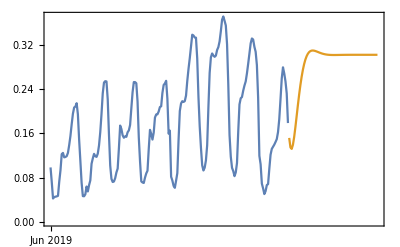

```mathematica
rescaledSubtractedtsmodelDLP=DateListPlot[{TimeSeriesWindow[rescaledSubtractedTS,{DateObject[{2019,6,1}],DateObject[{2019,8,24}]}],rescaledSubtractedforecast}]
```